Get::noopen: Cannot open MaTeX`.

# Numerical solutions for quark-antiquark meson Regge trajectories using Bohr-Sommerfeld semiclassical quantization

The analytical solution using the approximation of considering the masses of the quarks negligible and the potential linear. So the Hamiltonian in the CM reference frame is M=2p+σr. And the analytical solution is M^2=4σ(n+1/2).

## Bohr-Sommerfeld semiclassical quantization for a more general potential

The generalized potential in this case is . Once computed the integral let’s invert the function and plot it to compare it with the original solution.

InverseFunction::ifun: Inverse functions are being used. Values may be lost for multivalued inverses.

(#3 (-1+ProductLog[ⅇ^(1+(π (1+2 #1))/#3)]))/#2&

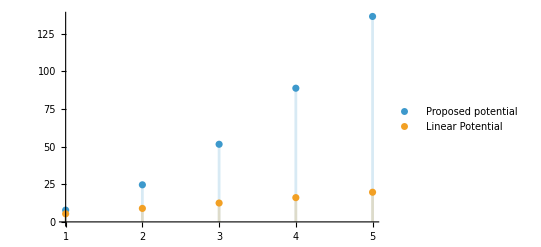

```mathematica
M=InverseFunction[1/(2*Pi)((#2-1/(#1/#3+1/#2))(#1+#3/#2)+#3Log[#1*#2/#3+1])-1/2&,1,3]
g=RandomReal[];
r0=RandomReal[10];
sigma=g/r0;
DiscretePlot[{M[x,r0,g]^2,4sigma*Pi(x+0.5)}, {x,5},PlotLegends->{"Proposed potential","Linear Potential"}]
```

Well, that doesn’t fit, does it :(

## General Potential renormalized

We try renormalizing by taking the potential at  and then taking the  of the result.

InverseFunction::ifun: Inverse functions are being used. Values may be lost for multivalued inverses.

(#3 (-#2+#4+#2 ProductLog[ⅇ^(1+(π (1+2 #1))/#3)]))/(#2 (#2-#4))&

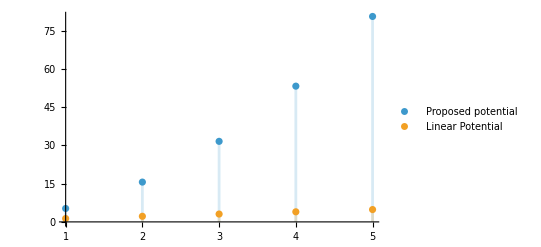

```mathematica
M=InverseFunction[1/(2*Pi)((#2-#4-1/(#1/#3+1/#2))(#1+#3/#2)+#3Log[(#1/#3+1/#2)*(#2-#4)])-1/2&,1,4]
g=RandomReal[];
r0=RandomReal[10];
sigma=g/r0;
DiscretePlot[{M[x,r0,g,0]^2,4sigma*Pi(x+0.5)}, {x,5},PlotLegends->{"Proposed potential","Linear Potential"}]
```

## General potential with lower bound for r

We take now the lower bound for r as .

InverseFunction::ifun: Inverse functions are being used. Values may be lost for multivalued inverses.

(#2 #3 ProductLog[ⅇ^(1/#2^2+π/#3+(2 π #1)/#3)])/(-1+#2^2)&

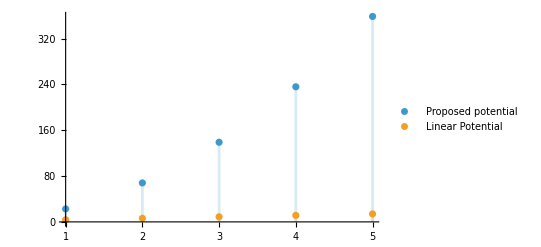

```mathematica
M=InverseFunction[1/(2*Pi)((#2-1/#2-1/(#1/#3+1/#2))(#1+#3/#2)+#3Log[(#2-1/#2)*(#1/#3)])-1/2&,1,3]
g=RandomReal[];
r0=RandomReal[10];
sigma=g/r0;
DiscretePlot[{M[x,r0,g]^2,4sigma*Pi(x+0.5)}, {x,5},PlotLegends->{"Proposed potential","Linear Potential"}]
```

## Bohr-Sommerfeld semiclassical quantization taking into account the mass of the quarks

Now the new Hamiltonian in CM reference frame is:

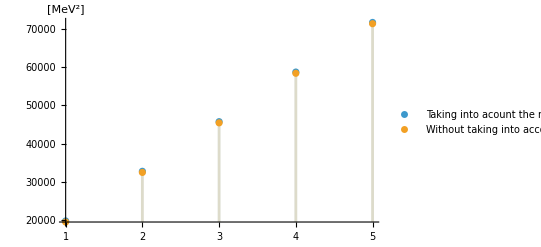

{0.0143684,0.00924591,0.00689915,0.00553762,0.00464301}

```mathematica
M=InverseFunction[-1/(2#2Pi) Integrate[Sqrt[(x^4-2(#3^2+#4^2)x^2+(#3^2+#4^2)^2-#3^2#4^2)/(x^2+(#3^2+#4^2))],{x,#1,(#3+#4)}]-1/2&,1,4];
sig=139.57^2/(6Pi);
m1=2.16;
m2=4.7;
DiscretePlot[{M[x,sig,m1,m2]^2,4sig*Pi(x+0.5)},{x,5},PlotLegends->{"Taking into acount the mass of the quarks.","Without taking into account the mass of the quarks"},AxesLabel->{"","[MeV^2]"}]
Table[Abs[(M[x,sig,m1,m2]^2-4sig*Pi(x+0.5))/(4sig*Pi(x+0.5))],{x,{1,2,3,4,5}}]
```

It works, yeey :D

## Dependance on g of the Regge trajectory for the proposed potential

Now we fix   and we keep  as a free parameter, and we plot it for several values of  to see how much it changes.

InverseFunction::ifun: Inverse functions are being used. Values may be lost for multivalued inverses.

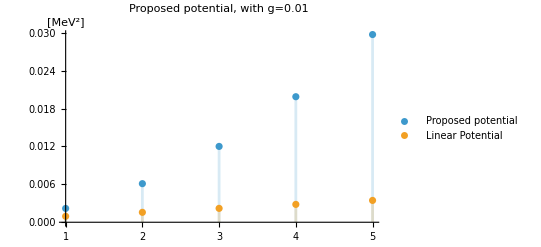
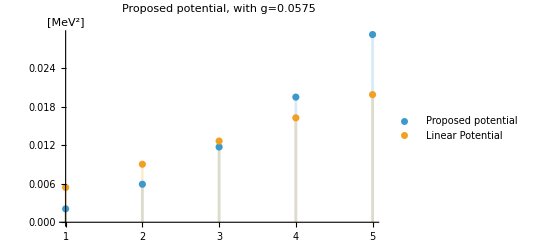
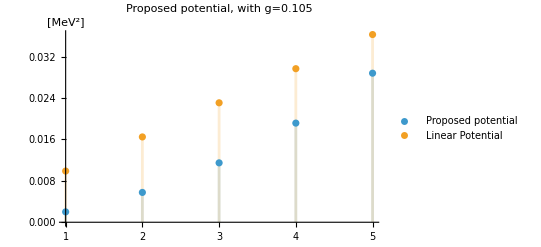
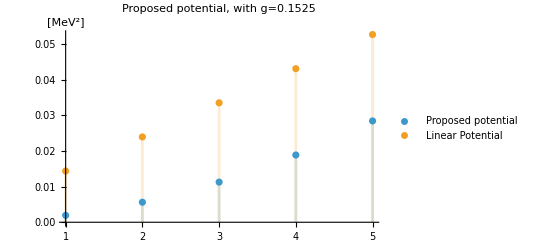
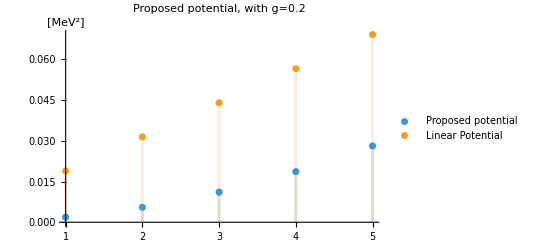

```mathematica
M=InverseFunction[1/(2*Pi)((#2-1/(#1/#3+1/#2))(#1+#3/#2)+#3Log[#1*#2/#3+1])-1/2&,1,3];
g=Array[# &,5,{0.01,0.2}];
glabels={StringJoin["Proposed potential, with g=",ToString[#] ]}&;
labelsg=Append[Flatten[Array[glabels,5,{0,0.2}]],"Lineal Potenital"];
r0=200;
sigma=#/r0 &;
Array[DiscretePlot[{M[x,r0,#]^2,4sigma[#]*Pi(x+0.5)},{x,5},PlotLegends->{"Proposed potential","Linear Potential"},AxesLabel->{"","[MeV^2]"},PlotLabel->StringJoin["Proposed potential, with g=",ToString[#]]]&,5,{0.01,0.2}]
```

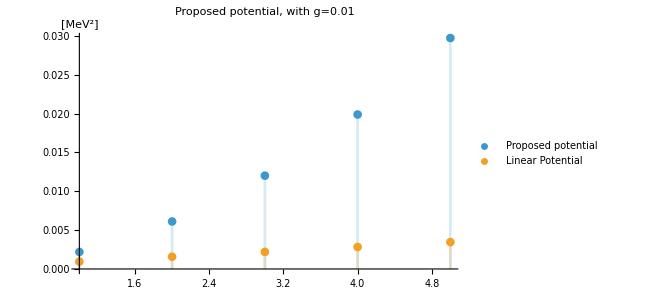
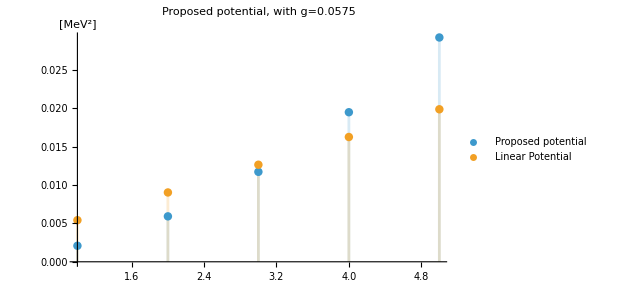
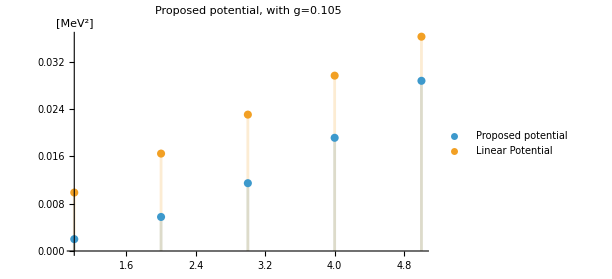
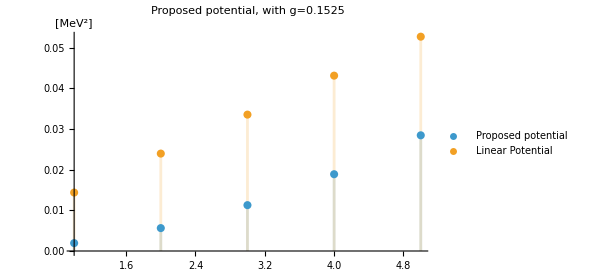
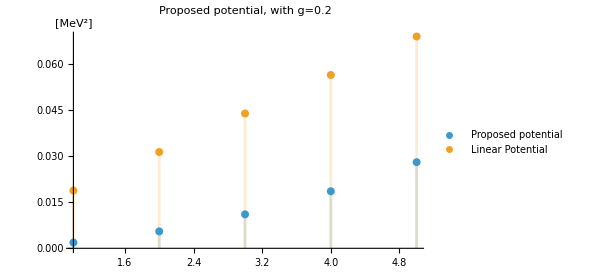

## Cornell Potential

Now we use the following potential: , i.e. a coulomb potential for higher energies (perturbative) and a string potential for lower energies (non perturbative). As the potential is divergent at  we will use the minimum value of  as , as a new free parameter. Let’s obtain now the Regge trajectory.

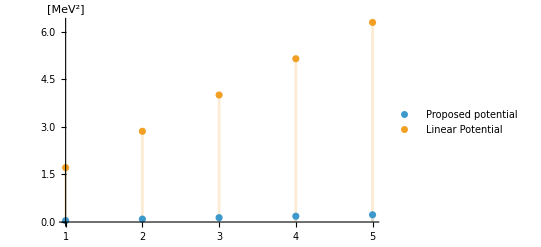

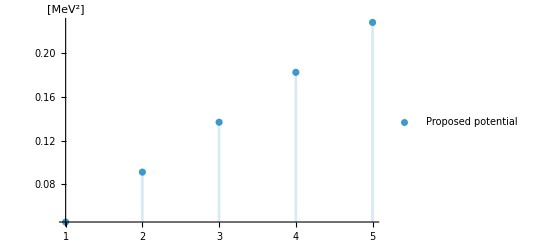

```mathematica
M=InverseFunction[1/2(#1(#1/#2(1+Sqrt[1+(4#2#3)/#1^2])-#4)-#3Log[#1/(#2#4)(1+Sqrt[1+(4#2#3)/#1^2])]+#2/2((#1/#2(1+Sqrt[1+(4#2#3)/#1^2]))^2-#4^2))&,1,4];
A=0;
r0=1/100000000000000000000;
sigma=RandomReal[];
DiscretePlot[{M[x,sigma,A,r0]^2,4sigma*Pi(x+0.5)},{x,5},PlotLegends->{"Proposed potential","Linear Potential"},AxesLabel->{"","[MeV^2]"}]
DiscretePlot[{M[x,sigma,A,r0]^2},{x,5},PlotLegends->{"Proposed potential"},AxesLabel->{"","[MeV^2]"}]
```